## TC Hamiltonian

```mathematica
(*Constants*)
bsize=20;ω0=1.0; ωc = 1.0; K = 2;j = 0.1;
(*Identity matrices for TLS and QHO*)
idTSS=SparseArray[IdentityMatrix[2]];
idHO=SparseArray[IdentityMatrix[bsize]];

(*TLS initial Hamiltonian*)
H0TSS=SparseArray[Band[{1,1}]->{ω0/2,-ω0/2}];
(*QHO Hamiltonian*)
H0HO=ωc * SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*TLS raising and lowering operators*)
σm={{0,0},{1,0}};
σp={{0,1},{0,0}};

(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 

(*Scaled harmonic oscillator Hamiltonian, using convention with TLS on the left.*)
Htot = KroneckerProduct[IdentityMatrix[2^K], H0HO];

Do[
(*Tensor product adjustment for the i-th TLS*)
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
(*TLS Hamiltonian for the i-th TLS*)
H0TSSi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,H0TSS],Sequence@@rightIds];
(*Print[Normal[H0TSSi]//MatrixForm];*)
(*Adding ith TLS Hamiltonian to the total Hamiltonian*)
Htot+=KroneckerProduct[H0TSSi,idHO];


σpi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σp],Sequence@@rightIds];σmi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σm],Sequence@@rightIds];
Htot+=j*(KroneckerProduct[σpi,a]+KroneckerProduct[σmi,a†]);
,{i,K}];
```

### Initial State

```mathematica
ψ0[w_,x0_]=1/Sqrt[Sqrt[ π]w] Exp[-(x-x0)^2/(2 w^2)];(*Define initial Gaussian state*)
EigState[n_, x_]=π^(-1/4)/Sqrt[2^n n!] Exp[-x^2/2]HermiteH[n,x];
coeff[n_,w_,x0_]:=NIntegrate[EigState[n, x]ψ0[w,x0],{x,-∞,∞},PrecisionGoal->6,AccuracyGoal->5]
ψ0HO=Table[coeff[n,1,2],{n,0,bsize-1}];

(*excited states in TSS and Gaussian in the QHO*)
ψ0Vec=KroneckerProduct[{1,0}, {1,0},ψ0HO]//Flatten;
```

### Observable Matrices

```mathematica
xM=KroneckerProduct[IdentityMatrix[2^K],1/Sqrt[2](a†+a)];(*Position of the oscillator*)
(*Expected x value for initial state*)
ConjugateTranspose[ψ0Vec].xM.ψ0Vec
```

2.

### Propagation

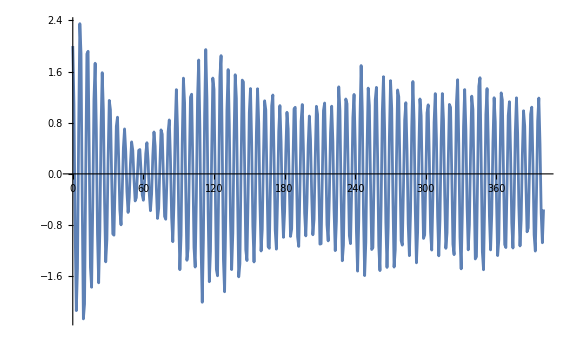

```mathematica
stateVector[t_] := MatrixExp[-I * Htot * t, ψ0Vec];
tMax =400; 
tRange=Range[0,tMax,1.0];
ψs=ParallelTable[stateVector[t],{t,tRange}];
xAve=Table[Conjugate[ψs[[n]]].xM.ψs[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,xAve//Re}//Transpose]
```